-108.55+0.00113679 x

-5.13494+0.0001174 x+6.03912×10^-10 x^2

-1.40767+0.0000152309 x+7.89524×10^-10 x^2-6.82285×10^-17 x^3

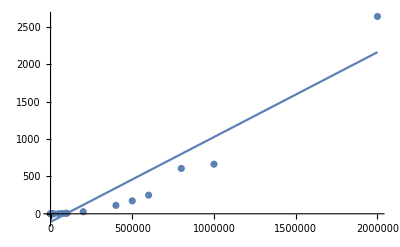

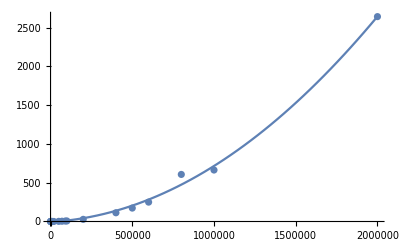

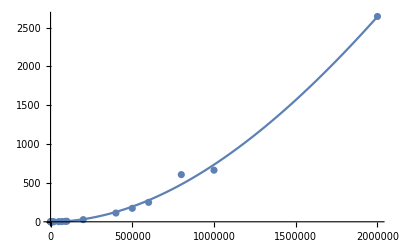

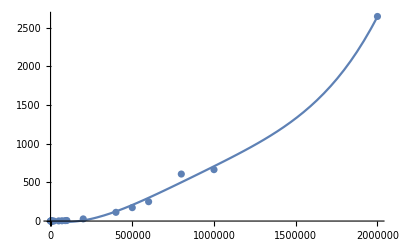

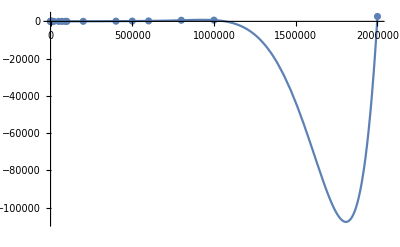

```mathematica
Insercion1=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x},x]

Insercion2=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x,x^2},x]

Insercion3=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x,x^2,x^3},x]

Insercion4=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x,x^2,x^3,x^4},x]

Insercion8=Fit[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

puntos=ListPlot[{{100,0.000008106231689453125},{500,0.000162125},{1000,0.000674963},{2000,0.003072977},{5000,0.018060923},{8000,0.054053068},{9000,0.109266996},{10000,0.075917959},{20000,0.278568983},{50000,1.918298006},{70000,3.448814869},{90000,5.771109104},{100000,6.984402895},{200000,27.77281809},{400000,112.6822109},{500000,173.109576},{600000,249.995821},{800000,607.273253},{1000000,664.1499751},{2000000,2643.314136}}]

g1=Plot[Insercion1,{x,0,2000000}]
Show[puntos,g1,PlotRange->All]

g2=Plot[Insercion2,{x,0,2000000}]
Show[puntos,g2,PlotRange->All]

g3=Plot[Insercion3,{x,0,2000000}]
Show[puntos,g3,PlotRange->All]

g4=Plot[Insercion4,{x,0,2000000}]
Show[puntos,g4,PlotRange->All]

g8=Plot[Insercion8,{x,0,2000000}]
Show[puntos,g8,PlotRange->All]
```